## Atomic to Physical Unit Conversions

```mathematica
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."]
(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."]
(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."]
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

## Inner Turning Point Integral

```mathematica
Clear[f,W,zi,zf,z]
f=0*fAU1mVcm;
W=0*enAU1GHz;
zi=0;
zf=6;
Integrate[1/(2*(W+1/z+f*z))^(1/2),{z,zi,zf}]
```

4 √3

```mathematica
4*√3/tAU1ns
```

1.67585×10^-7

## Turning Times vs. Launch Energy and Field

### Uphill

```mathematica
Clear[W,f,z,zi,zt,t,results]
W=200*enAU1GHz;
f=200*fAU1mVcm;
zi=-6;
zt=-1/(2*f)*(W+√(W^2+4*f));
t=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];
Print["t: ",t/tAU1ns,"\t θ: ",Arg[t]]
```

t: 4.70751	 θ: 0

### Uphill Bulk

```mathematica
(* Atomic to Physical Unit Conversions *)
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
(* Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."] *)
(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
(* Print["1 ns = ",tAU1ns, " A.U."] *)
(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
(* Print["1 mV/cm = ",fAU1mVcm," A.U."] *)
(* Execute *)
Clear[f];
Monitor[Do[
Clear[W,z,zi,zt,t,results];
tidy=Function[{x},ToString[FortranForm[N[x]]]];
SetDirectory[NotebookDirectory[]];
(* Parallel Execution *)
results={};
SetSharedVariable[results];
tstart=AbsoluteTime[];
(* f=1*fAU1mVcm; *)
(* W=0*enAU1GHz; *)
zi=-6;
ParallelDo[
zt=-1/(2*f)*(W+√(W^2+4*f));
t=NIntegrate[(-1/√(2*(W-1/z+f*z))),{z,zi,zt}];
AppendTo[results,{W,f,zt,Re[t],Arg[t]}]
,{W,Table[i*enAU1GHz,{i,-200,200,1}]}];
tend=AbsoluteTime[];
(* Export *)
fname="results\\"<>StringReplace[DateString[Now,"ISODateTime"],":"->"-"]<>".txt";
header=StringJoin[
"# Filename\t"<>Directory[]<>fname<>"\n",
"# Source\t"<>NotebookFileName[]<>"\n",
"# Note\t"<>"1D calculation of turning time vs. field and orbit energy."<>"\n",
"# Date\t"<>DateString[Now,"ISODateTime"]<>"\n",
"# Dir\t"<>"-1"<>"\n",
"# field\t"<>tidy[f]<>"\n",
"# zi\t"<>tidy[zi]<>"\n",
"W"<>"\t"<>"field"<>"\t"<>"zt"<>"\t"<>"t"<>"\t"<>"argt"<>"\n"
];
Put[fname];
stream=OpenWrite[fname];
WriteString[stream,header]
Do[
wstring=StringJoin[
tidy[results[[i,1]]],"\t",
tidy[results[[i,2]]],"\t",
tidy[results[[i,3]]],"\t",
tidy[results[[i,4]]],"\t",
tidy[results[[i,5]]],"\n"];
WriteString[stream,wstring]
,{i,1,Dimensions[results][[1]]}
];
Close[stream];
,{f,Table[i*fAU1mVcm,{i,1,300,1}]}],f/fAU1mVcm]
```

```mathematica
3.3*300/(60*60)
```

0.275

```mathematica
Now
```

Mon 5 Feb 2018 05:22:39GMT-5.

```mathematica
results
```

```mathematica
ListPlot[{results[[All,1]],results[[All,4]]/tAU1ns},Joined->True]
```

```mathematica
(* Print["zi: ",zi,"\t zt ",zt]
Print[Re[t]/tAU1ns,"\t",t,"\t Θ(t):",Arg[t]] *)
```

### Downhill

## Scratch

```mathematica
Arg[-10+1.*I]
```

3.04192

```mathematica
Clear[W,z,f]
Solve[W-1/z+f*z==0,z]
```

{{z→(-W-√(4 f+W^2))/(2 f)},{z→(-W+√(4 f+W^2))/(2 f)}}

```mathematica
Clear[f,W,z,soln,solp]
cond={W->-100*enAU1GHz,f->10*fAU1mVcm};
(* soln=Solve[0==f*z^2+W*z-1,z]; *)
soln=Solve[W==1/z-f*z,z];
(* solp=Solve[0==f*z^2+W*z+1,z]; *)
solp=Solve[W==-1/z-f*z,z];
Print["z < 0 \t",soln]
Print["z < 0 \t",soln/.cond]
Print["z > 0 \t",solp]
Print["z > 0 \t",solp/.cond]
```

z < 0 	{{z→(-W-√(4 f+W^2))/(2 f)},{z→(-W+√(4 f+W^2))/(2 f)}}

z < 0 	{{z→-65252.},{z→7.88053×10^6}}

z > 0 	{{z→(-W-√(-4 f+W^2))/(2 f)},{z→(-W+√(-4 f+W^2))/(2 f)}}

z > 0 	{{z→66360.3},{z→7.74892×10^6}}

```mathematica
Clear[f,W,z]
W=-100*enAU1GHz;
f=10*fAU1mVcm;
(-W-√(4*f+W^2))/(2*f)
```

-65252.

```mathematica
Clear[f,W,z]
W=-100*enAU1GHz;
f=10*fAU1mVcm;
NSolve[0==W+1/z-f*z,z]
NSolve[0==W-1/z-f*z,z]
```

{{z→-7.88053×10^6},{z→65252.}}

{{z→-7.74892×10^6},{z→-66360.3}}

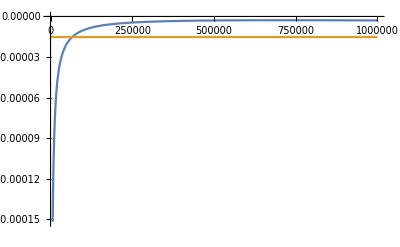

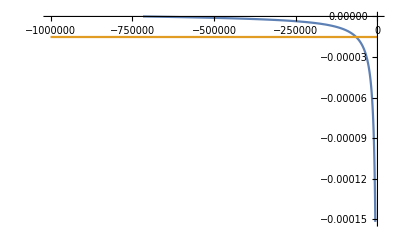

```mathematica
Clear[f,W,z]
W=-100*enAU1GHz;
f=10*fAU1mVcm;
Plot[{-1/z-f*z,W},{z,0,1000000},PlotRange->{All,{10W,0}}]
Plot[{1/z-f*z,W},{z,-1000000,0},PlotRange->{All,{10W,0}}]
```